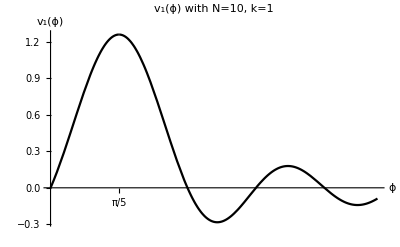

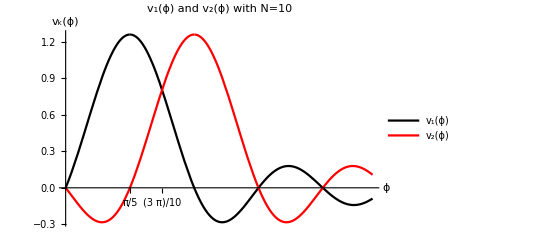

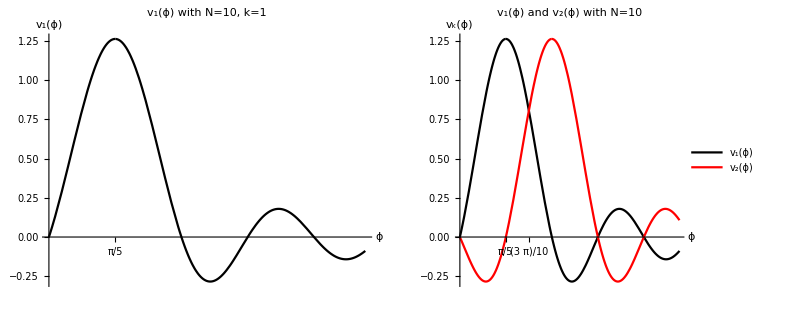

```mathematica
v[k_, t_, n_]:= (2 Pi n)^(-1/2)Sin[n/2(t-(2 Pi k)/n)]/Sin[1/2(t-(2 Pi k)/n)]
plot1 = Plot[{v[1,t,10],Line[{{1,1},{2,2}}]},{t,0,3}, PlotStyle->Black, AxesLabel->{ϕ,Subscript[v, 1][ϕ]}, PlotLabel-> "v_1(ϕ) with N=10, k=1", Ticks -> {{2Pi/10},None}, ImagePadding->20]
plot2 = Plot[{v[1,t,10],v[2,t,10]},{t,0,3},PlotStyle->{Black,Red},AxesLabel->{ϕ,Subscript[v, k][ϕ]},PlotLabel->"v_1(ϕ) and v_2(ϕ) with N=10", Ticks->{{2Pi/10,3Pi/10},None},PlotLegends->Placed[{"v_1(ϕ)", "v_2(ϕ)"},{Right,Top}],ImagePadding->20]
GraphicsRow[{plot1,plot2}]
```

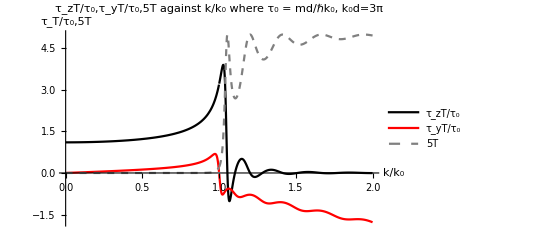

```mathematica
tz[r_]:=((1-2r^2)Sinh[3Pi Sqrt[1-r^2]]^2+3 Pi/2 Sqrt[1-r^2]Sinh[6Pi Sqrt[1-r^2]])/(3Pi(4r^2(1-r^2)^2+(1-r^2)Sinh[3Pi Sqrt[(1-r^2)]]^2))
ty[r_]:=r/(3Pi Sqrt[1-r^2])((6Pi Sqrt[1-r^2](1-2r^2)+Sinh[6Pi Sqrt[1-r^2]])/(4r^2+Sinh[3Pi Sqrt[1-r^2]]^2))
tr[r_]:=1/(1+(Sinh[3Pi Sqrt[1-r^2]]^2)/(4r^2(1-r^2)))
plot3 =Plot[{tz[r],ty[r],5tr[r]},{r,0,2},PlotStyle->{Black,Red,{Gray,Dashed}},AxesLabel->{"k/k_0","τ_T/τ_0,5T"},PlotLabel->"τ_zT/τ_0,τ_yT/τ_0,5T against k/k_0 where τ_0 = md/ℏk_0, k_0d=3π",PlotLegends->Placed[{"τ_zT/τ_0","τ_yT/τ_0","5T"},{Left,Top}]]
```

```mathematica
A[k_,k0_]=Integrate[1/Sqrt[2Pi] Exp[-x^2+I k0 x]Exp[-I k x],{x,-Infinity,Infinity}]
A[k,k0]
```

(ⅇ^(-1/4 (k-k0)^2))/(√2)

(ⅇ^(-1/4 (k-k0)^2))/(√2)

```mathematica
dispersion[m]=Series[k^2/(2m),{k,k0,1}]
```

k0^2/(2 m)+(k0 (k-k0))/m+O[k-k0]^2

```mathematica
psi[x_,t_,k0_,m_]=Integrate[1/Sqrt[2Pi] A[k,k0]Exp[I(k x - (k0^2/(2m)+(k0 (k-k0))/m) t)],{k,-Infinity,Infinity}]
```

ⅇ^(-(k0^2 t (ⅈ m+2 t))/(2 m^2)+(k0 (ⅈ m+2 t) x)/m-x^2)

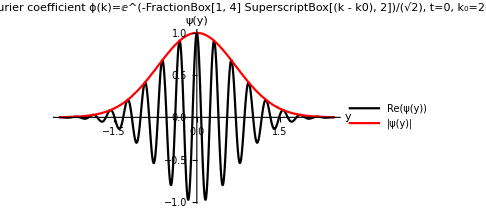

```mathematica
plot4=Plot[{Re[psi[x,0,20,1]],Abs[psi[x,0,10,1]]},{x,-2.5,2.5},PlotRange->All,PlotStyle->{Black,Red},AxesLabel->{"y","ψ(y)"},PlotLabel->"Gaussian Wavepacket with Fourier coefficient \nϕ(k)=ⅇ^(-FractionBox[1, 4] SuperscriptBox[(k - k0), 2])/(√2), t=0, k_0=20, m=1 (ℏ=1)",PlotLegends->Placed[{"Re(ψ(y))", "|ψ(y)|"},{Left,Top}],ImageSize->Medium]
```

```mathematica
Export["/Users/jamespuleston/Documents/Cambridge/Essay/TunnellingTimesInQuantumMechanics/Mathematica/plot1.pdf",GraphicsRow[{plot1,plot2}]]
Export["/Users/jamespuleston/Documents/Cambridge/Essay/TunnellingTimesInQuantumMechanics/Mathematica/plot3.pdf",plot3]
Export["/Users/jamespuleston/Documents/Cambridge/Essay/TunnellingTimesInQuantumMechanics/Mathematica/plot4.pdf",plot4]
```

/Users/jamespuleston/Documents/Cambridge/Essay/TunnellingTimesInQuantumMechanics/Mathematica/plot1.pdf

/Users/jamespuleston/Documents/Cambridge/Essay/TunnellingTimesInQuantumMechanics/Mathematica/plot3.pdf

/Users/jamespuleston/Documents/Cambridge/Essay/TunnellingTimesInQuantumMechanics/Mathematica/plot4.pdf